```mathematica
df[f_,r_]:=f''[r]-l1(2r f'[r]+(r^2-l2)f[r])/(r^2(r^2-l1))+f[r];
fs[z0_,s_]:=Function[z,(z-z0)^s Sum[b[n](z-z0)^n,{n, 0, ∞}]];
```

```mathematica
tmp=df[fs[√l1,0],r]//FullSimplify
```

1/(-l1 r^2+r^4)((-l1 r^2+r^4) ∑_(n=0)^∞ (-1+n) n (-√l1+r)^(-2+n) b[n]-2 l1 r ∑_(n=0)^∞ n (-√l1+r)^(-1+n) b[n]+(l1 l2-2 l1 r^2+r^4) ∑_(n=0)^∞ (-√l1+r)^n b[n])

```mathematica
Series[tmp,{r,√l1,5}]//Normal
```

∑_(n=0)^∞ (-1+n) n (-√l1+r)^(-2+n) b[n]+(3/(2 √l1)-1/(-√l1+r)-(7 (-√l1+r))/(4 l1)+(15 (-√l1+r)^2)/(8 l1^(3/2))-(31 (-√l1+r)^3)/(16 l1^2)+(63 (-√l1+r)^4)/(32 l1^(5/2))) ∑_(n=0)^∞ n (-√l1+r)^(-1+n) b[n]+((5 (l1-l2))/(4 l1)+(-l1+l2)/(2 √l1 (-√l1+r))+((-l1+17 l2) (-√l1+r))/(8 l1^(3/2))+((l1-49 l2) (-√l1+r)^2)/(16 l1^2)+((-l1+129 l2) (-√l1+r)^3)/(32 l1^(5/2))+((l1-321 l2) (-√l1+r)^4)/(64 l1^3)) ∑_(n=0)^∞ (-√l1+r)^n b[n]

Допуская, что умножение рядов возможно, внесем (r-√l1) в суммы.

```mathematica
∑_(n=0)^∞ (-1+n) n (-√l1+r)^(-2+n) b[n]+(3/(2 √l1)∑_(n=0)^∞ n (-√l1+r)^(-1+n) b[n]-∑_(n=0)^∞ n (-√l1+r)^(-2+n) b[n]-(7 ∑_(n=0)^∞ n (-√l1+r)^n b[n])/(4 l1)+(15 ∑_(n=0)^∞ n (-√l1+r)^(+1+n) b[n])/(8 l1^(3/2))-(31 ∑_(n=0)^∞ n (-√l1+r)^(2+n) b[n])/(16 l1^2)+(63 ∑_(n=0)^∞ n (-√l1+r)^(+3+n) b[n])/(32 l1^(5/2))) +((5 (l1-l2))/(4 l1)∑_(n=0)^∞ (-√l1+r)^n b[n]+(-l1+l2)/(2 √l1)∑_(n=0)^∞ (-√l1+r)^(n-1) b[n]+((-l1+17 l2) ∑_(n=0)^∞ (-√l1+r)^(n+1) b[n])/(8 l1^(3/2))+((l1-49 l2) ∑_(n=0)^∞ (-√l1+r)^(n+2) b[n])/(16 l1^2)+((-l1+129 l2) ∑_(n=0)^∞ (-√l1+r)^(n+3) b[n])/(32 l1^(5/2))+((l1-321 l2) ∑_(n=0)^∞ (-√l1+r)^(n+4) b[n])/(64 l1^3)) ;
```

Поменяем индексы в суммах, чтобы внутри остались только члены вида (r-√l1)^n.

```mathematica
∑_(n=-2)^∞ (1+n) (n+2) (-√l1+r)^n b[n+2]+(3/(2 √l1)∑_(n=-1)^∞ (n+1) (-√l1+r)^n b[n+1]-∑_(n=-2)^∞ (n+2) (-√l1+r)^n b[n+2]-(7 ∑_(n=0)^∞ n (-√l1+r)^n b[n])/(4 l1)+(15 ∑_(n=1)^∞ (n-1) (-√l1+r)^n b[n-1])/(8 l1^(3/2))-(31 ∑_(n=2)^∞ (n-2) (-√l1+r)^n b[n-2])/(16 l1^2)+(63 ∑_(n=3)^∞ (n-3) (-√l1+r)^n b[n-3])/(32 l1^(5/2))) +((5 (l1-l2))/(4 l1)∑_(n=0)^∞ (-√l1+r)^n b[n]+(-l1+l2)/(2 √l1)∑_(n=-1)^∞ (-√l1+r)^n b[n+1]+((-l1+17 l2) ∑_(n=1)^∞ (-√l1+r)^n b[n-1])/(8 l1^(3/2))+((l1-49 l2) ∑_(n=2)^∞ (-√l1+r)^n b[n-2])/(16 l1^2)+((-l1+129 l2) ∑_(n=3)^∞ (-√l1+r)^n b[n-3])/(32 l1^(5/2))+((l1-321 l2) ∑_(n=4)^∞ (-√l1+r)^n b[n-4])/(64 l1^3)) ;
```

Рассмотрим член перед (r-l1)^n. Это выражение справедливо для n >= 5.

```mathematica
(((l1-321 l2) (-√l1+r)^n b[-4+n])/(64 l1^3)+((-l1+129 l2)(-√l1+r)^n b[-3+n])/(32 l1^(5/2))+(63 (-3+n) (-√l1+r)^n b[-3+n])/(32 l1^(5/2))+((l1-49 l2) (-√l1+r)^n b[-2+n])/(16 l1^2)-(31 (-2+n) (-√l1+r)^n b[-2+n])/(16 l1^2)+((-l1+17 l2) (-√l1+r)^n b[-1+n])/(8 l1^(3/2))+(15 (-1+n) (-√l1+r)^n b[-1+n])/(8 l1^(3/2))+(5 (l1-l2) (-√l1+r)^n b[n])/(4 l1)-(7 n (-√l1+r)^n b[n])/(4 l1)+((-l1+l2) (-√l1+r)^n b[1+n])/(2 √l1)+(3 (1+n) (-√l1+r)^n b[1+n])/(2 √l1)-(2+n) (-√l1+r)^n b[2+n]+(1+n) (2+n) (-√l1+r)^n b[2+n])/(-√l1+r)^n  //FullSimplify
```

1/(64 l1^3)((l1-321 l2) b[-4+n]+2 √l1 (-(189+l1-129 l2-63 n) b[-3+n]+2 √l1 ((62+l1-49 l2-31 n) b[-2+n]-2 √l1 (15+l1-17 l2-15 n) b[-1+n]+4 l1 (5 l1-5 l2-7 n) b[n])+16 l1^2 (3-l1+l2+3 n) b[1+n])+64 l1^3 n (2+n) b[2+n])

Отсюда можно получить решение для b[n+2] через b[n+1], b[n], b[n-1], b[n-2], b[n-3], b[n-4].

```mathematica
bs[n+2]=(b[2+n]/.First@Solve[%==0,b[2+n]]/.b->bs//FullSimplify)
```

-1/(64 l1^3 n (2+n))((l1-321 l2) bs[-4+n]+2 √l1 (-(189+l1-129 l2-63 n) bs[-3+n]+2 √l1 ((62+l1-49 l2-31 n) bs[-2+n]-2 √l1 (15+l1-17 l2-15 n) bs[-1+n]+4 l1 (5 l1-5 l2-7 n) bs[n])+16 l1^2 (3-l1+l2+3 n) bs[1+n]))

Однако для n < 5 подход должен быть другим.

```mathematica
tmpser=Series[tmp/.∞->9//FullSimplify,{r,√l1,10}]
```

(-l1 b[0]+l2 b[0]-2 √l1 b[1])/(2 √l1 (r-√l1))+(5 l1 b[0]-5 l2 b[0]+6 √l1 b[1]-2 l1^(3/2) b[1]+2 √l1 l2 b[1])/(4 l1)+1/(8 l1^(3/2))(-l1 b[0]+17 l2 b[0]-14 √l1 b[1]+10 l1^(3/2) b[1]-10 √l1 l2 b[1]+24 l1 b[2]-4 l1^2 b[2]+4 l1 l2 b[2]+24 l1^(3/2) b[3]) (r-√l1)+1/(16 l1^2)(l1 b[0]-49 l2 b[0]+30 √l1 b[1]-2 l1^(3/2) b[1]+34 √l1 l2 b[1]-56 l1 b[2]+20 l1^2 b[2]-20 l1 l2 b[2]+72 l1^(3/2) b[3]-8 l1^(5/2) b[3]+8 l1^(3/2) l2 b[3]+128 l1^2 b[4]) (r-√l1)^2+((129 (-l1^2 b[0]+l1 l2 b[0]-2 l1^(3/2) b[1]))/(32 l1^(7/2))-(49 (-2 l1 b[1]-l1^2 b[1]+l1 l2 b[1]))/(16 l1^3)+(17 (4 l1 b[0]+6 l1 b[2]-l1^2 b[2]+l1 l2 b[2]+6 l1^(3/2) b[3]))/(8 l1^(5/2))-(5 (4 √l1 b[0]+4 l1 b[1]+8 √l1 b[2]+24 l1 b[3]-l1^2 b[3]+l1 l2 b[3]+16 l1^(3/2) b[4]))/(4 l1^2)+(b[0]+4 √l1 b[1]+2 b[2]+4 l1 b[2]+24 √l1 b[3]+52 l1 b[4]-l1^2 b[4]+l1 l2 b[4]+30 l1^(3/2) b[5])/(2 l1^(3/2))) (r-√l1)^3+(-(321 (-l1^2 b[0]+l1 l2 b[0]-2 l1^(3/2) b[1]))/(64 l1^4)+(129 (-2 l1 b[1]-l1^2 b[1]+l1 l2 b[1]))/(32 l1^(7/2))-(49 (4 l1 b[0]+6 l1 b[2]-l1^2 b[2]+l1 l2 b[2]+6 l1^(3/2) b[3]))/(16 l1^3)+(17 (4 √l1 b[0]+4 l1 b[1]+8 √l1 b[2]+24 l1 b[3]-l1^2 b[3]+l1 l2 b[3]+16 l1^(3/2) b[4]))/(8 l1^(5/2))-(5 (b[0]+4 √l1 b[1]+2 b[2]+4 l1 b[2]+24 √l1 b[3]+52 l1 b[4]-l1^2 b[4]+l1 l2 b[4]+30 l1^(3/2) b[5]))/(4 l1^2)+(b[1]+4 √l1 b[2]+6 b[3]+4 l1 b[3]+48 √l1 b[4]+90 l1 b[5]-l1^2 b[5]+l1 l2 b[5]+48 l1^(3/2) b[6])/(2 l1^(3/2))) (r-√l1)^4+((769 (-l1^2 b[0]+l1 l2 b[0]-2 l1^(3/2) b[1]))/(128 l1^(9/2))-(321 (-2 l1 b[1]-l1^2 b[1]+l1 l2 b[1]))/(64 l1^4)+(129 (4 l1 b[0]+6 l1 b[2]-l1^2 b[2]+l1 l2 b[2]+6 l1^(3/2) b[3]))/(32 l1^(7/2))-(49 (4 √l1 b[0]+4 l1 b[1]+8 √l1 b[2]+24 l1 b[3]-l1^2 b[3]+l1 l2 b[3]+16 l1^(3/2) b[4]))/(16 l1^3)+(17 (b[0]+4 √l1 b[1]+2 b[2]+4 l1 b[2]+24 √l1 b[3]+52 l1 b[4]-l1^2 b[4]+l1 l2 b[4]+30 l1^(3/2) b[5]))/(8 l1^(5/2))-(5 (b[1]+4 √l1 b[2]+6 b[3]+4 l1 b[3]+48 √l1 b[4]+90 l1 b[5]-l1^2 b[5]+l1 l2 b[5]+48 l1^(3/2) b[6]))/(4 l1^2)+(b[2]+4 √l1 b[3]+12 b[4]+4 l1 b[4]+80 √l1 b[5]+138 l1 b[6]-l1^2 b[6]+l1 l2 b[6]+70 l1^(3/2) b[7])/(2 l1^(3/2))) (r-√l1)^5+(-(1793 (-l1^2 b[0]+l1 l2 b[0]-2 l1^(3/2) b[1]))/(256 l1^5)+(769 (-2 l1 b[1]-l1^2 b[1]+l1 l2 b[1]))/(128 l1^(9/2))-(321 (4 l1 b[0]+6 l1 b[2]-l1^2 b[2]+l1 l2 b[2]+6 l1^(3/2) b[3]))/(64 l1^4)+(129 (4 √l1 b[0]+4 l1 b[1]+8 √l1 b[2]+24 l1 b[3]-l1^2 b[3]+l1 l2 b[3]+16 l1^(3/2) b[4]))/(32 l1^(7/2))-(49 (b[0]+4 √l1 b[1]+2 b[2]+4 l1 b[2]+24 √l1 b[3]+52 l1 b[4]-l1^2 b[4]+l1 l2 b[4]+30 l1^(3/2) b[5]))/(16 l1^3)+(17 (b[1]+4 √l1 b[2]+6 b[3]+4 l1 b[3]+48 √l1 b[4]+90 l1 b[5]-l1^2 b[5]+l1 l2 b[5]+48 l1^(3/2) b[6]))/(8 l1^(5/2))-(5 (b[2]+4 √l1 b[3]+12 b[4]+4 l1 b[4]+80 √l1 b[5]+138 l1 b[6]-l1^2 b[6]+l1 l2 b[6]+70 l1^(3/2) b[7]))/(4 l1^2)+(b[3]+4 √l1 b[4]+20 b[5]+4 l1 b[5]+120 √l1 b[6]+196 l1 b[7]-l1^2 b[7]+l1 l2 b[7]+96 l1^(3/2) b[8])/(2 l1^(3/2))) (r-√l1)^6+((4097 (-l1^2 b[0]+l1 l2 b[0]-2 l1^(3/2) b[1]))/(512 l1^(11/2))-(1793 (-2 l1 b[1]-l1^2 b[1]+l1 l2 b[1]))/(256 l1^5)+(769 (4 l1 b[0]+6 l1 b[2]-l1^2 b[2]+l1 l2 b[2]+6 l1^(3/2) b[3]))/(128 l1^(9/2))-(321 (4 √l1 b[0]+4 l1 b[1]+8 √l1 b[2]+24 l1 b[3]-l1^2 b[3]+l1 l2 b[3]+16 l1^(3/2) b[4]))/(64 l1^4)+(129 (b[0]+4 √l1 b[1]+2 b[2]+4 l1 b[2]+24 √l1 b[3]+52 l1 b[4]-l1^2 b[4]+l1 l2 b[4]+30 l1^(3/2) b[5]))/(32 l1^(7/2))-(49 (b[1]+4 √l1 b[2]+6 b[3]+4 l1 b[3]+48 √l1 b[4]+90 l1 b[5]-l1^2 b[5]+l1 l2 b[5]+48 l1^(3/2) b[6]))/(16 l1^3)+1/(8 l1^(5/2))17 (b[2]+4 √l1 b[3]+12 b[4]+4 l1 b[4]+80 √l1 b[5]+138 l1 b[6]-l1^2 b[6]+l1 l2 b[6]+70 l1^(3/2) b[7])-1/(4 l1^2)5 (b[3]+4 √l1 b[4]+20 b[5]+4 l1 b[5]+120 √l1 b[6]+196 l1 b[7]-l1^2 b[7]+l1 l2 b[7]+96 l1^(3/2) b[8])+(b[4]+4 √l1 b[5]+30 b[6]+4 l1 b[6]+168 √l1 b[7]+264 l1 b[8]-l1^2 b[8]+l1 l2 b[8]+126 l1^(3/2) b[9])/(2 l1^(3/2))) (r-√l1)^7+(-(9217 (-l1^2 b[0]+l1 l2 b[0]-2 l1^(3/2) b[1]))/(1024 l1^6)+(4097 (-2 l1 b[1]-l1^2 b[1]+l1 l2 b[1]))/(512 l1^(11/2))-(1793 (4 l1 b[0]+6 l1 b[2]-l1^2 b[2]+l1 l2 b[2]+6 l1^(3/2) b[3]))/(256 l1^5)+(769 (4 √l1 b[0]+4 l1 b[1]+8 √l1 b[2]+24 l1 b[3]-l1^2 b[3]+l1 l2 b[3]+16 l1^(3/2) b[4]))/(128 l1^(9/2))-(321 (b[0]+4 √l1 b[1]+2 b[2]+4 l1 b[2]+24 √l1 b[3]+52 l1 b[4]-l1^2 b[4]+l1 l2 b[4]+30 l1^(3/2) b[5]))/(64 l1^4)+(129 (b[1]+4 √l1 b[2]+6 b[3]+4 l1 b[3]+48 √l1 b[4]+90 l1 b[5]-l1^2 b[5]+l1 l2 b[5]+48 l1^(3/2) b[6]))/(32 l1^(7/2))-1/(16 l1^3)49 (b[2]+4 √l1 b[3]+12 b[4]+4 l1 b[4]+80 √l1 b[5]+138 l1 b[6]-l1^2 b[6]+l1 l2 b[6]+70 l1^(3/2) b[7])+1/(8 l1^(5/2))17 (b[3]+4 √l1 b[4]+20 b[5]+4 l1 b[5]+120 √l1 b[6]+196 l1 b[7]-l1^2 b[7]+l1 l2 b[7]+96 l1^(3/2) b[8])-1/(4 l1^2)5 (b[4]+4 √l1 b[5]+30 b[6]+4 l1 b[6]+168 √l1 b[7]+264 l1 b[8]-l1^2 b[8]+l1 l2 b[8]+126 l1^(3/2) b[9])+(b[5]+4 √l1 b[6]+42 b[7]+4 l1 b[7]+224 √l1 b[8]+342 l1 b[9]-l1^2 b[9]+l1 l2 b[9])/(2 l1^(3/2))) (r-√l1)^8+((20481 (-l1^2 b[0]+l1 l2 b[0]-2 l1^(3/2) b[1]))/(2048 l1^(13/2))-(9217 (-2 l1 b[1]-l1^2 b[1]+l1 l2 b[1]))/(1024 l1^6)+(4097 (4 l1 b[0]+6 l1 b[2]-l1^2 b[2]+l1 l2 b[2]+6 l1^(3/2) b[3]))/(512 l1^(11/2))-(1793 (4 √l1 b[0]+4 l1 b[1]+8 √l1 b[2]+24 l1 b[3]-l1^2 b[3]+l1 l2 b[3]+16 l1^(3/2) b[4]))/(256 l1^5)+(769 (b[0]+4 √l1 b[1]+2 b[2]+4 l1 b[2]+24 √l1 b[3]+52 l1 b[4]-l1^2 b[4]+l1 l2 b[4]+30 l1^(3/2) b[5]))/(128 l1^(9/2))-(321 (b[1]+4 √l1 b[2]+6 b[3]+4 l1 b[3]+48 √l1 b[4]+90 l1 b[5]-l1^2 b[5]+l1 l2 b[5]+48 l1^(3/2) b[6]))/(64 l1^4)+1/(32 l1^(7/2))129 (b[2]+4 √l1 b[3]+12 b[4]+4 l1 b[4]+80 √l1 b[5]+138 l1 b[6]-l1^2 b[6]+l1 l2 b[6]+70 l1^(3/2) b[7])-1/(16 l1^3)49 (b[3]+4 √l1 b[4]+20 b[5]+4 l1 b[5]+120 √l1 b[6]+196 l1 b[7]-l1^2 b[7]+l1 l2 b[7]+96 l1^(3/2) b[8])+(b[6]+4 √l1 b[7]+56 b[8]+4 l1 b[8]+288 √l1 b[9])/(2 l1^(3/2))+1/(8 l1^(5/2))17 (b[4]+4 √l1 b[5]+30 b[6]+4 l1 b[6]+168 √l1 b[7]+264 l1 b[8]-l1^2 b[8]+l1 l2 b[8]+126 l1^(3/2) b[9])-(5 (b[5]+4 √l1 b[6]+42 b[7]+4 l1 b[7]+224 √l1 b[8]+342 l1 b[9]-l1^2 b[9]+l1 l2 b[9]))/(4 l1^2)) (r-√l1)^9+(-(45057 (-l1^2 b[0]+l1 l2 b[0]-2 l1^(3/2) b[1]))/(4096 l1^7)+(20481 (-2 l1 b[1]-l1^2 b[1]+l1 l2 b[1]))/(2048 l1^(13/2))-(9217 (4 l1 b[0]+6 l1 b[2]-l1^2 b[2]+l1 l2 b[2]+6 l1^(3/2) b[3]))/(1024 l1^6)+(4097 (4 √l1 b[0]+4 l1 b[1]+8 √l1 b[2]+24 l1 b[3]-l1^2 b[3]+l1 l2 b[3]+16 l1^(3/2) b[4]))/(512 l1^(11/2))-1/(256 l1^5)1793 (b[0]+4 √l1 b[1]+2 b[2]+4 l1 b[2]+24 √l1 b[3]+52 l1 b[4]-l1^2 b[4]+l1 l2 b[4]+30 l1^(3/2) b[5])+(769 (b[1]+4 √l1 b[2]+6 b[3]+4 l1 b[3]+48 √l1 b[4]+90 l1 b[5]-l1^2 b[5]+l1 l2 b[5]+48 l1^(3/2) b[6]))/(128 l1^(9/2))-1/(64 l1^4)321 (b[2]+4 √l1 b[3]+12 b[4]+4 l1 b[4]+80 √l1 b[5]+138 l1 b[6]-l1^2 b[6]+l1 l2 b[6]+70 l1^(3/2) b[7])+1/(32 l1^(7/2))129 (b[3]+4 √l1 b[4]+20 b[5]+4 l1 b[5]+120 √l1 b[6]+196 l1 b[7]-l1^2 b[7]+l1 l2 b[7]+96 l1^(3/2) b[8])-(5 (b[6]+4 √l1 b[7]+56 b[8]+4 l1 b[8]+288 √l1 b[9]))/(4 l1^2)+(b[7]+4 √l1 b[8]+72 b[9]+4 l1 b[9])/(2 l1^(3/2))-1/(16 l1^3)49 (b[4]+4 √l1 b[5]+30 b[6]+4 l1 b[6]+168 √l1 b[7]+264 l1 b[8]-l1^2 b[8]+l1 l2 b[8]+126 l1^(3/2) b[9])+(17 (b[5]+4 √l1 b[6]+42 b[7]+4 l1 b[7]+224 √l1 b[8]+342 l1 b[9]-l1^2 b[9]+l1 l2 b[9]))/(8 l1^(5/2))) (r-√l1)^10+O[r-√l1]^11

Найдем выражения для первых нескольких коэффициентов.

```mathematica
SeriesCoefficient[tmpser,-1]
bs1[1]=b[1]/.First@Solve[SeriesCoefficient[tmpser,-1]==0,b[1]]/.b->bs//FullSimplify
bs1[1]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify
```

(-l1 b[0]+l2 b[0]-2 √l1 b[1])/(2 √l1)

((-l1+l2) bs[0])/(2 √l1)

bs[0]/(√(-2+l+l^2))

```mathematica
SeriesCoefficient[tmpser,0]
bs2[1]=b[1]/.First@Solve[SeriesCoefficient[tmpser,0]==0,b[1]]/.b->bs//FullSimplify
bs2[1]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify
```

(5 l1 b[0]-5 l2 b[0]+6 √l1 b[1]-2 l1^(3/2) b[1]+2 √l1 l2 b[1])/(4 l1)

(5 (l1-l2) bs[0])/(2 √l1 (-3+l1-l2))

bs[0]/(√(-2+l+l^2))

```mathematica
bs[1]=bs1[1];
```

```mathematica
SeriesCoefficient[tmpser,1]
bs[3]=b[3]/.First@Solve[SeriesCoefficient[tmpser,1]==0,b[3]]/.b->bs//FullSimplify
bs[3]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify
```

1/(8 l1^(3/2))(-l1 b[0]+17 l2 b[0]-14 √l1 b[1]+10 l1^(3/2) b[1]-10 √l1 l2 b[1]+24 l1 b[2]-4 l1^2 b[2]+4 l1 l2 b[2]+24 l1^(3/2) b[3])

((5 l1^2+5 (-2+l2) l2-2 l1 (3+5 l2)) bs[0]+4 l1 (-6+l1-l2) bs[2])/(24 l1^(3/2))

-(2 (bs[0]+2 bs[2]))/(3 √(-2+l+l^2))

```mathematica
SeriesCoefficient[tmpser,2]
bs[4]=b[4]/.First@Solve[SeriesCoefficient[tmpser,2]==0,b[4]]/.b->bs//FullSimplify
bs[4]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify
```

1/(16 l1^2)(l1 b[0]-49 l2 b[0]+30 √l1 b[1]-2 l1^(3/2) b[1]+34 √l1 l2 b[1]-56 l1 b[2]+20 l1^2 b[2]-20 l1 l2 b[2]+72 l1^(3/2) b[3]-8 l1^(5/2) b[3]+8 l1^(3/2) l2 b[3]+128 l1^2 b[4])

1/(384 l1^2)((5 l1^3-3 l1^2 (18+5 l2)-(-2+l2) l2 (96+5 l2)+l1 (96+5 l2 (28+3 l2))) bs[0]+4 l1 (96+l1^2-2 l1 (15+l2)+l2 (30+l2)) bs[2])

(7 bs[0]+20 bs[2])/(12 (-2+l+l^2))

```mathematica
SeriesCoefficient[tmpser,3]
bs[5]=b[5]/.First@Solve[SeriesCoefficient[tmpser,3]==0,b[5]]/.b->bs//FullSimplify
bs[5]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify
```

(129 (-l1^2 b[0]+l1 l2 b[0]-2 l1^(3/2) b[1]))/(32 l1^(7/2))-(49 (-2 l1 b[1]-l1^2 b[1]+l1 l2 b[1]))/(16 l1^3)+(17 (4 l1 b[0]+6 l1 b[2]-l1^2 b[2]+l1 l2 b[2]+6 l1^(3/2) b[3]))/(8 l1^(5/2))-(5 (4 √l1 b[0]+4 l1 b[1]+8 √l1 b[2]+24 l1 b[3]-l1^2 b[3]+l1 l2 b[3]+16 l1^(3/2) b[4]))/(4 l1^2)+(b[0]+4 √l1 b[1]+2 b[2]+4 l1 b[2]+24 √l1 b[3]+52 l1 b[4]-l1^2 b[4]+l1 l2 b[4]+30 l1^(3/2) b[5])/(2 l1^(3/2))

1/(11520 l1^(5/2))((5 l1^4-2 l1^3 (157+10 l2)+(-2+l2) l2 (3168+l2 (356+5 l2))+2 l1^2 (924+l2 (487+15 l2))-2 l1 (1440+l2 (2152+l2 (503+10 l2)))) bs[0]+4 l1 (-2880+l1^3-l1^2 (82+3 l2)-l2 (1272+l2 (82+l2))+l1 (888+l2 (164+3 l2))) bs[2])

(-41 bs[0]-8 (13+l+l^2) bs[2])/(60 (-2+l+l^2)^(3/2))

```mathematica
SeriesCoefficient[tmpser,4]
bs[6]=b[6]/.First@Solve[SeriesCoefficient[tmpser,4]==0,b[6]]/.b->bs//FullSimplify
bs[6]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify
```

-(321 (-l1^2 b[0]+l1 l2 b[0]-2 l1^(3/2) b[1]))/(64 l1^4)+(129 (-2 l1 b[1]-l1^2 b[1]+l1 l2 b[1]))/(32 l1^(7/2))-(49 (4 l1 b[0]+6 l1 b[2]-l1^2 b[2]+l1 l2 b[2]+6 l1^(3/2) b[3]))/(16 l1^3)+(17 (4 √l1 b[0]+4 l1 b[1]+8 √l1 b[2]+24 l1 b[3]-l1^2 b[3]+l1 l2 b[3]+16 l1^(3/2) b[4]))/(8 l1^(5/2))-(5 (b[0]+4 √l1 b[1]+2 b[2]+4 l1 b[2]+24 √l1 b[3]+52 l1 b[4]-l1^2 b[4]+l1 l2 b[4]+30 l1^(3/2) b[5]))/(4 l1^2)+(b[1]+4 √l1 b[2]+6 b[3]+4 l1 b[3]+48 √l1 b[4]+90 l1 b[5]-l1^2 b[5]+l1 l2 b[5]+48 l1^(3/2) b[6])/(2 l1^(3/2))

1/(552960 l1^3)((5 l1^5-l1^4 (764+25 l2)+2 l1^3 (6654+l2 (1544+25 l2))-2 l1^2 (44280+l2 (26506+5 l2 (468+5 l2)))-(-2+l2) l2 (161280+l2 (28008+l2 (806+5 l2)))+l1 (138240+l2 (224544+l2 (66100+l2 (3152+25 l2))))) bs[0]+4 l1 (138240+l1^4-4 l1^3 (43+l2)+6 l1^2 (818+l2 (86+l2))-4 l1 (10620+l2 (3030+l2 (129+l2)))+l2 (77040+l2 (7212+l2 (172+l2)))) bs[2])

(2 (61+5 l (1+l)) bs[0]+3 (106+17 l (1+l)) bs[2])/(180 (-2+l+l^2)^2)

Замечаем, что b[0] можно положить равным 1. b[2] является параметром.

```mathematica
bs[0]=α;
bs[1]=bs[1]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify;
bs[2]=β;
bs[3]=bs[3]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify;
bs[4]=bs[4]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify;
bs[5]=bs[5]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify;
bs[6]=bs[6]/.{l1->(l-1)(l+2),l2->l(l+1)}//FullSimplify;
{ bs[0], bs[1], bs[2], bs[3], bs[4], bs[5], bs[6] }//FullSimplify
bs[n]=bs[n+2]/.{l1->(l-1)(l+2),l2->l(l+1),n->(n-2)}//FullSimplify
```

{α,α/(√(-2+l+l^2)),β,-(2 (α+2 β))/(3 √(-2+l+l^2)),(7 α+20 β)/(12 (-2+l+l^2)),(-41 α-8 (13+l+l^2) β)/(60 (-2+l+l^2)^(3/2)),(2 (61+5 l (1+l)) α+318 β+51 l (1+l) β)/(180 (-2+l+l^2)^2)}

-1/(64 (-2+l+l^2)^3 (-2+n) n)(-2 (1+160 l (1+l)) bs[-6+n]+2 √(-2+l+l^2) ((-313+128 l (1+l)+63 n) bs[-5+n]+2 √(-2+l+l^2) (-(-122+48 l (1+l)+31 n) bs[-4+n]+2 √(-2+l+l^2) (-43+16 l (1+l)+15 n) bs[-3+n]-4 (-2+l+l^2) (-4+7 n) bs[-2+n])+16 (-2+l+l^2)^2 (-1+3 n) bs[-1+n]))

Получим несколько более высоких коэффициентов.

```mathematica
(bs[n]/.{n->6})//FullSimplify
```

(2 (61+5 l (1+l)) α+318 β+51 l (1+l) β)/(180 (-2+l+l^2)^2)

```mathematica
(bs[n]/.{n->7})//FullSimplify
```

(-(-13225+16 l (1+l) (189+67 l (1+l))) α-96 (-1+l) (2+l) (186+47 l (1+l)) β)/(10080 (-2+l+l^2)^(7/2))

```mathematica
(bs[n]/.{n->8})/.{bs[7]->(bs[n]/.{n->7})}//FullSimplify
```

(3 (-141143+32 l (1+l) (1008+541 l (1+l))) α+2 (-1+l) (2+l) (272617+128 l (1+l) (759+7 l (1+l))) β)/(322560 (-2+l+l^2)^4)

Изобразим функцию для получения серии коэффициентов.

```mathematica
coeflist[len_]:=Module[{coefs},
coefs[0]=bs[0];coefs[1]=bs[1];coefs[2]=bs[2];
coefs[3]=bs[3];coefs[4]=bs[4];coefs[5]=bs[5];
Do[coefs[i]=((bs[n]/.n->i)/.Table[bs[j]->coefs[j],{j,i-6,i-1}])//N//Simplify//N,{i,6,len}];
Return[Array[coefs,len,{0,len-1}]];
];
```

```mathematica
coeflist[11]
```

{α,α/(√(-2+l+l^2)),β,-(2 (α+2 β))/(3 √(-2+l+l^2)),(7 α+20 β)/(12 (-2+l+l^2)),(-41 α-8 (13+l+l^2) β)/(60 (-2+l+l^2)^(3/2)),1/((-2.+l+l^2)^3)((-1.35556+0.566667 l+0.622222 l^2+0.111111 l^3+0.0555556 l^4) α+(-3.53333+1.2 l+1.48333 l^2+0.566667 l^3+0.283333 l^4) β),1/((-2.+l+l^2)^(7/2))((1.312-0.3 l-0.406349 l^2-0.212698 l^3-0.106349 l^4) α+(3.54286-0.87619 l-1.32381 l^2-0.895238 l^3-0.447619 l^4) β),1/((-2.+l+l^2)^5)(0.+(2.62543-1.91271 l-1.93474 l^2+0.116964 l^3+0.461012 l^4+0.483036 l^5+0.161012 l^6) α+(6.76133-4.35181 l-5.04878 l^2-0.813777 l^3+1.04906 l^4+1.7627 l^5+0.613492 l^6+0.0222222 l^7+0.00555556 l^8) β),1/((-2.+l+l^2)^(15/2))((-9.48809+15.2548 l+8.27467 l^2-14.498 l^3-7.49001 l^4+2.60231 l^5+5.09037 l^6+2.42163 l^7-0.904597 l^8-1.02607 l^9-0.224614 l^10-0.010582 l^11-0.00176367 l^12) α+(-25.0663+39.7031 l+22.699 l^2-36.5918 l^3-21.5024 l^4+4.73893 l^5+14.3147 l^6+7.71137 l^7-2.19425 l^8-2.92945 l^9-0.767284 l^10-0.0989418 l^11-0.0164903 l^12) β),1/((-2.+l+l^2)^12)(0.+(137.452-491.118 l+240.493 l^2+896.509 l^3-753.636 l^4-846.167 l^5+664.139 l^6+633.372 l^7-210.856 l^8-385.331 l^9-73.5448 l^10+147.353 l^11+94.0767 l^12-18.9865 l^13-33.0916 l^14-6.14646 l^15+3.3353 l^16+1.73685 l^17+0.353272 l^18+0.0506173 l^19+0.00506173 l^20) α+(359.299-1263.96 l+566.527 l^2+2325.15 l^3-1759.25 l^4-2265.93 l^5+1414.47 l^6+1759.88 l^7-251.663 l^8-1068.21 l^9-375.806 l^10+381.395 l^11+314.27 l^12-28.6777 l^13-96.5009 l^14-24.9405 l^15+6.65323 l^16+5.30767 l^17+1.62261 l^18+0.326168 l^19+0.0326168 l^20) β)}

Изобразим функцию, представляемую рядом с этими коэффициентами.

```mathematica
fs2[coefs_,l0_,a_,b_]:=Function[r,Sum[N@(coefs[[n+1]]/.{l->l0,α->a,β->b})(r-N@√((l0-1)(l0+2)))^n,{n,0,Length[coefs]-1}]];
```

```mathematica
plotfs2[n_,l_,a_,b_]:=Module[{coefs},coefs=coeflist[n]//N;Plot[fs2[coefs,l,a,b][r],{r,0.5 √((l-1)(l+2)),2 √((l-1)(l+2))}]];
```

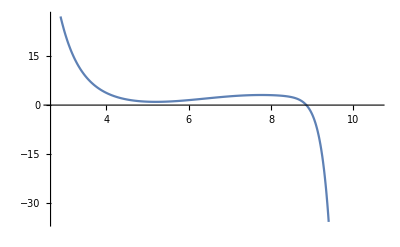

```mathematica
plotfs2[20,5,1,1]
```